# Revisión numérica de la analítica de la matriz de Choi y su pureza

## 0.1. Packages loading and nb definitions

```mathematica
SetDirectory[NotebookDirectory[]];
Get["../Mathematica_packages/"<>#]&/@{"Chaometer.wl","QMB.wl"};
```

```mathematica
(* Canal completamente depolarizante que actúa sobre el primer espín de una cadena de N espines *)
DepolarizingChannel[ρ_,L_]:=
Module[{kraus},
(* Construir operadores de Kraus *)
kraus=KroneckerProduct[#,IdentityMatrix[2^(L-1)]]&/@ArrayReshape[IdentityMatrix[4]/√2,{4,2,2}];

(* Aplicar canal en su forma de Kraus a ρ *)
Total[#.ρ.ConjugateTranspose[#]&/@kraus]
]
```

```mathematica
(* Funciones para implementar cada uno de los términos de eq:appendix:A:2 *)
t1EqAppA2[t_,ψ0E_,eigenvalsH_,eigenvecsH_]:=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]/4

t2EqAppA2[t_,ψ0E_,eigenvalsH_,eigenvecsH_]:=-2*Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]/4

t3EqAppA2[t_,ψ0E_,eigenvalsH_,eigenvecsH_]:=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]/4
```

```mathematica
(* Ticks personalizados para las gráficas en escala log *)
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
myTicks=Join[labeledTicks,unlabeledTicks];
```

## 1. Revisión de expresión analítica de la pureza de la matriz de Choi

## 1.1 Parameters setup

```mathematica
L=11(*number of spins*);
{hx,hz,J}={1.,0.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,0.5,{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=Table[RandomChainProductState[L-1],3];
```

```mathematica
superoperators=ToExpression[Import["/home/jadeleon/Documents/quantum_chaotic_channels/ja_files/chaotic/superoperators_2.csv"][[2;;]](*la primera fila tiene la info*)];
```

```mathematica
(* Check de que un superoperador random sea el correcto comparando con la construccion de alguno  *)
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *);
MatrixForm[Round[#,10.^-7]]&/@{Chop@Superoperator[t,ψ0E[[2]](*número de estado aleatorio*),eigenvalsH,eigenvecsH,L],superoperators[[t/0.1+1]]}
Equal@@%
```

{(0.493083 | 0.0122412+0.0119287 ⅈ | 0.0122412-0.0119287 ⅈ | 0.475635
0.0182229+0.0081882 ⅈ | 0.0410292-0.006847 ⅈ | 0.0367151+0.0005877 ⅈ | -0.0344784+0.0009147 ⅈ
0.0182229-0.0081882 ⅈ | 0.0367151-0.0005877 ⅈ | 0.0410292+0.006847 ⅈ | -0.0344784-0.0009147 ⅈ
0.506917 | -0.0122412-0.0119287 ⅈ | -0.0122412+0.0119287 ⅈ | 0.524365),(0.493083 | 0.0122412+0.0119287 ⅈ | 0.0122412-0.0119287 ⅈ | 0.475635
0.0182229+0.0081882 ⅈ | 0.0410292-0.006847 ⅈ | 0.0367151+0.0005877 ⅈ | -0.0344784+0.0009147 ⅈ
0.0182229-0.0081882 ⅈ | 0.0367151-0.0005877 ⅈ | 0.0410292+0.006847 ⅈ | -0.0344784-0.0009147 ⅈ
0.506917 | -0.0122412-0.0119287 ⅈ | -0.0122412+0.0119287 ⅈ | 0.524365)}

True

```mathematica
chois=1/2*Reshuffle/@superoperators;
```

```mathematica
choiPurities=Transpose[{Range[0,50,0.1],Chop[Purity/@chois]}];
```

### Buscando una matriz de Choi con 3 eigenvalores distintos de cero

En t=0.1 la matriz de Choi tiene 3 eigenvalores distintos de cero:

```mathematica
Chop[Eigenvalues/@chois][[1;;10]]
```

{{1.,0,0,0},{0.990571,0.00942882,7.1102×10^-10,0},{0.962127,0.0378731,1.611×10^-7,6.34061×10^-9},{0.917729,0.0822674,3.61008×10^-6,3.2418×10^-7},{0.864172,0.135792,0.0000311566,4.93318×10^-6},{0.810132,0.189672,0.000158488,0.0000378668},{0.76307,0.236173,0.000572634,0.000184883},{0.725874,0.271861,0.00161379,0.000650498},{0.695952,0.298531,0.00373108,0.00178679},{0.668433,0.320188,0.00732188,0.00405679}}

```mathematica
Select[Chop[Eigenvalues/@chois],Count[#,x_/;x==0]==1&]
```

{{0.990571,0.00942882,7.1102×10^-10,0}}

```mathematica
Table[{t,Chop@Eigenvalues[1/2Reshuffle[Superoperator[t,ψ0E[[1]],eigenvalsH,eigenvecsH,L]]]},{t,Power[10.,Range[-1,0,0.1]]}]
```

{{0.1,{0.990941,0.00905903,1.02617×10^-9,0}},{0.125893,{0.985525,0.0144751,6.35322×10^-9,0}},{0.158489,{0.976908,0.0230921,3.90888×10^-8,9.23572×10^-10}},{0.199526,{0.963309,0.0366906,2.38371×10^-7,9.07454×10^-9}},{0.251189,{0.942179,0.0578193,1.43501×10^-6,8.80243×10^-8}},{0.316228,{0.91027,0.0897205,8.4763×10^-6,8.35387×10^-7}},{0.398107,{0.864572,0.135371,0.0000486914,7.62972×10^-6}},{0.501187,{0.805695,0.193971,0.000269064,0.0000649}},{0.630957,{0.746266,0.251834,0.00142095,0.000479169}},{0.794328,{0.715535,0.274624,0.00716329,0.00267805}},{1.,{0.706809,0.252229,0.0310831,0.0098782}}}

```mathematica
TableForm[Chop@,TableHeadings->{None,{Style[TraditionalForm[HoldForm[t]],20],Text[Style["Choi eigenvalues",Black,20]]}},TableSpacing->{5,2}]
```

t | Choi eigenvalues
0.1 | 0.990941
0.00905903
1.02617×10^-9
0
0.125893 | 0.985525
0.0144751
6.35322×10^-9
0
0.158489 | 0.976908
0.0230921
3.90888×10^-8
9.23572×10^-10
0.199526 | 0.963309
0.0366906
2.38371×10^-7
9.07454×10^-9
0.251189 | 0.942179
0.0578193
1.43501×10^-6
8.80243×10^-8
0.316228 | 0.91027
0.0897205
8.4763×10^-6
8.35387×10^-7
0.398107 | 0.864572
0.135371
0.0000486914
7.62972×10^-6
0.501187 | 0.805695
0.193971
0.000269064
0.0000649
0.630957 | 0.746266
0.251834
0.00142095
0.000479169
0.794328 | 0.715535
0.274624
0.00716329
0.00267805
1. | 0.706809
0.252229
0.0310831
0.0098782

## 1.1. Matriz de choi

```mathematica
MatrixForm@Table[
{q,r}=IntegerDigits[i,2,2]+1;{p,s}=IntegerDigits[j,2,2]+1;
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{s-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{r-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]/2
,{i,0,3},{j,0,3}]
```

(0.246192+0. ⅈ | 0.0154966+0.00356999 ⅈ | -0.000178027-0.00466358 ⅈ | 0.00614217+0.00118478 ⅈ
0.0154966-0.00356999 ⅈ | 0.246958+0. ⅈ | 0.0100395+0.00520072 ⅈ | -0.022327-0.00607428 ⅈ
-0.000178027+0.00466358 ⅈ | 0.0100395-0.00520072 ⅈ | 0.253808+0. ⅈ | -0.0154966-0.00356999 ⅈ
0.00614217-0.00118478 ⅈ | -0.022327+0.00607428 ⅈ | -0.0154966+0.00356999 ⅈ | 0.253042+0. ⅈ)

```mathematica
MatrixForm[chois[[t/0.1+1]]]
```

(0.246192 | 0.0154966+0.00356999 ⅈ | -0.000178027-0.00466358 ⅈ | 0.00614217+0.00118478 ⅈ
0.0154966-0.00356999 ⅈ | 0.246958 | 0.0100395+0.00520072 ⅈ | -0.022327-0.00607428 ⅈ
-0.000178027+0.00466358 ⅈ | 0.0100395-0.00520072 ⅈ | 0.253808 | -0.0154966-0.00356999 ⅈ
0.00614217-0.00118478 ⅈ | -0.022327+0.00607428 ⅈ | -0.0154966+0.00356999 ⅈ | 0.253042)

## 1.2. Pureza de la matriz de Choi

```mathematica
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *)
```

13.4

### eq:choi:chaometer:purity:1

```mathematica
(*  Calcular {pureza numérica, pureza analítica con eq:choi:chaometer:purity:1} *)
{Select[choiPurities,#[[1]]==t&],Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,q}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2/4
,{i,2},{j,2},{p,2},{q,2}]}
```

{{{13.4,0.252964}},0.252964}

### eq:choi:chaometer :purity:2 (Echo de Loschmidt)

```mathematica
(* Calcular la pureza analítica con eq:choi:chaometer:purity:2, echo de Loshcmidt *)
ψ1=StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{#}],ψ0E[[2]]],eigenvalsH,eigenvecsH]&/@{0,1};
ρ1=Total[Dyad[#]&/@ψ1]/2;(* U (I/2 ⊗ ψψ) U^† *)
ρ2=DepolarizingChannel[ρ1,L];
Chop@Total[Braket[#,ρ2.#]&/@ψ1]
```

0.252964

### eq:appendix:A:1

```mathematica
(* Calcular el primer término dentro del paréntesis de eq:appendix:A:1 *)
t1=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,p}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

1.00299

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:1 *)
t2=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

0.00958805

```mathematica
{Select[choiPurities,#[[1]]==t&],(t1+t2)/4}
```

{{{46.6,0.253144}},0.253144}

### eq:appendix:A:2

```mathematica
(* Calcular el primer término dentro del paréntesis de eq:appendix:A:2 para confirmar que es igual a 2 *)
t1=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]
```

2.

```mathematica
(* Calcular la suma de los primeros dos términos dentro del paréntesis de eq:appendix:A:2. Debería ser igual al primer término de eq:appendix:A:1 *)
t2=-2*Sum[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]
,{i,2},{j,2}]
```

-0.997548+0. ⅈ

```mathematica
(* Calcular el tercer término dentro del paréntesis de eq:appendix:A:2 *)
t3=Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{p,Mod[p+1,2,1]}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2},{p,2}]
```

0.00933467

```mathematica
(* Calcular la suma de todos los términos para revisar que sí de la pureza *)
{Select[choiPurities,#[[1]]==t&],(t1+t2+t3)/4}
```

{{{13.5,0.252947}},0.252947+0. ⅈ}

### eq:appendix:A:3

Es necesario revisar nada más el tercer término porque los primeros dos son iguales a los de la ecuación eq:appendix:A:2.

Sí son iguales los terceros términos de las ecuaciones eq:appendix:A:2 y eq:appendix:A:3

```mathematica
t=RandomChoice[Range[0,50,0.1]](* un tiempo aleatorio *)
```

46.6

```mathematica
(* Calcular el tercer término de la ecuación eq:appendix:A:3 *)
1/2*Sum[
Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E[[2]]],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]
```

0.00239701

```mathematica
(* Calcular el tercer término de la ecuación eq:appendix:A:2 *)
t3EqAppA2[t,ψ0E[[2]],eigenvalsH,eigenvecsH]
```

0.00239701

## 2. Investigando la pureza de la matriz de Choi (L=11 espines)

Estamos investigando la expresión analítica de la pureza de la matriz de Choi^1

^1eq:appendix:A:2 en las notas

## 2.1. Pureza con Hamiltoniano GOE

Obtener un Hamiltoniano del ensamble ortogonal gausiano (GOE) y revisar cómo se comportan el segundo y tercer término de la expresión analítica de la pureza de la matriz de Choi (eq:appendix:A:2 o eq:appendix:A:2).

La investigación numérica sugiere que, en la región caótica:
 -∑_(i,j) Re(i,ψ_(0E)U^†(t)(00⊗𝟙_E)U(t)j,ψ_(0E)j,ψ_(0E)U^†(t)(1  1⊗𝟙_E)U(t)i,ψ_(0E))=-1/4, t≫1
 
 ∑_(i,j) |i,ψ_(0E)U^†(t)(01⊗𝟙_E)U(t)j,ψ_(0E)|^2=0, t≫1

### 2.1.1. Cálculos

```mathematica
L=11;(* número de espines *) 

(* Obtener un Hamiltoniano de GOE y calcular sus eigenvalores y eigenvectores *)
Module[{H},
H=RandomVariate[GaussianOrthogonalMatrixDistribution[2^L]];
{eigenvalsH,eigenvecsH}=Chop[Eigensystem[H]];
]
```

```mathematica
(* Definir un estado inicial aleatorio para el entorno de L-1 espines *)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:2 *)
t2=Table[t2EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

```mathematica
(*tercer término pureza matriz de Choi *)
t3=Table[t3EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

### 2.1.2. Gráfica

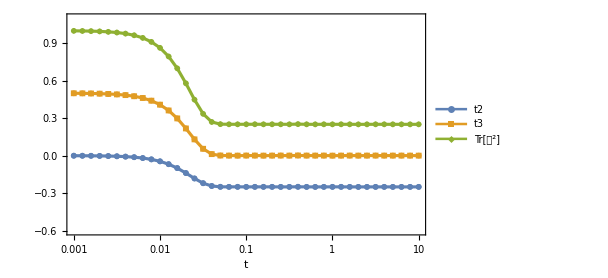

```mathematica
ListLogLinearPlot[Transpose[{Power[10.,Range[-3,1,0.1]],#}]&/@{t2,t3,(1/2+t2+t3)},
PlotRange->{{10^(-3),10},{-0.6,1.1}}(*----*),
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
PlotMarkers->{Automatic,6},
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Table[y,{y,-0.5,1,0.25}]},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],None},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->450,
PlotLegends->{"t2","t3",TraditionalForm[HoldForm[Tr[𝒟^2]]]}
]
```

## 2.2. Pureza con Hamiltoniano con P(s) Poissoniana

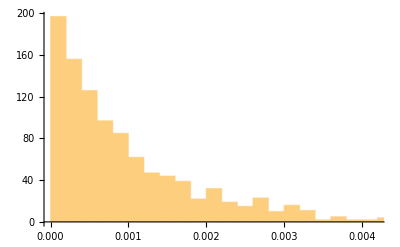

```mathematica
(*Set the size of the matrix*)
n=2^L;

(*Create a diagonal matrix with uniformly distributed random entries*)
d=DiagonalMatrix[RandomReal[{0,1},n]];

(*Optionally,apply a random unitary transformation*)
A=RandomComplex[{-1,1},{n,n}]; (*Generate a random complex matrix*)
{U,R}=QRDecomposition[A];
RandomMatrix=Transpose[U].d.U;

(*Get the eigenvalues*)
eigenvalues=Eigenvalues[RandomMatrix];

(*Plot the level spacing distribution*)
Histogram[Differences[Sort[Chop@eigenvalues]]]
```

```mathematica
(*Set the size of the matrix*)
n=2^L;

(*Create a diagonal matrix with uniformly distributed random entries*)
eigenvalsH=RandomReal[{0,1},n];

(*Optionally,apply a random unitary transformation*)
A=RandomComplex[{-1,1},{n,n}]; (*Generate a random complex matrix*)
{U,R}=QRDecomposition[A];
eigenvecsH=Transpose[U];
```

```mathematica
(* Revisar que los eigenvectores esten normalizados *)
AllTrue[Norm/@eigenvecsH,#==1.&]
```

True

```mathematica
(* Definir un estado inicial para el entorno de L-1 espines *)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:2 *)
t2=Table[t2EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

```mathematica
(*tercer término pureza matriz de Choi *)
t3=Table[t3EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,1,0.1]]}];
```

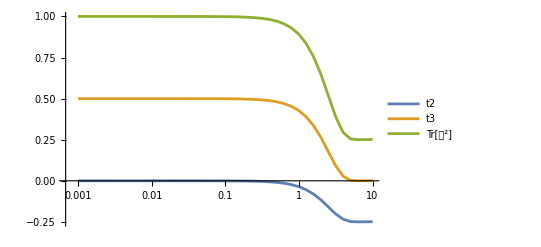

```mathematica
ListLogLinearPlot[Transpose[{Power[10.,Range[-3,1,0.1]],#}]&/@{t2/4,t3/4,(2+t2+t3)/4},
Joined->True,
PlotLegends->{"t2","t3",TraditionalForm[HoldForm[Tr[𝒟^2]]]}
]
```

## 2.3. Región regular (h_x=J=1,h_z=2.5)

Investigamos cómo se comportan el segundo y tercer término de la expresión analítica de Tr(𝒟^2) (eq:appendix:A:2 o eq:appendix:A:2) en la región regular.

La investigación numérica sugiere que, en la región regular, el segundo término de la expresión analítica de Tr(𝒟^2) se hace aproximadamente cero en todo momento.

### 2.3.1. Cálculos

```mathematica
L=9(*number of spins*);
{hx,hz,J}={1.,2.5,ConstantArray[1.,L-1]}(*hz=0.5 chaotic, hz=2.5 regular*)
```

{1.,2.5,{1.,1.,1.,1.,1.,1.,1.,1.}}

```mathematica
Module[{H},
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];
]
```

```mathematica
(*Three initial random states of the environment Subscript[ψ, 0E]=Subscript[random, 1]⊗…⊗Subscript[random, L-1]*)
SeedRandom[32371];
ψ0E=RandomChainProductState[L-1];
```

```mathematica
(* Calcular el segundo término dentro del paréntesis de eq:appendix:A:2 *)
t2=Table[t2EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,2,0.1]]}];
```

$Aborted

```mathematica
(*tercer término pureza matriz de Choi *)
t3=Table[t3EqAppA2[t,ψ0E,eigenvalsH,eigenvecsH],{t,Power[10.,Range[-3,2,0.1]]}];
```

```mathematica
(* Ticks personalizados para las gráficas en escala log *)
labeledTicks=Table[{10^i,Superscript[10,i]},{i,-20,15}];
unlabeledTicks=Flatten[Table[{k*j,Null},{k,2,9},{j,labeledTicks[[All,1]]}],1];
myTicks=Join[labeledTicks,unlabeledTicks];
```

### 2.3.2. Gráfica

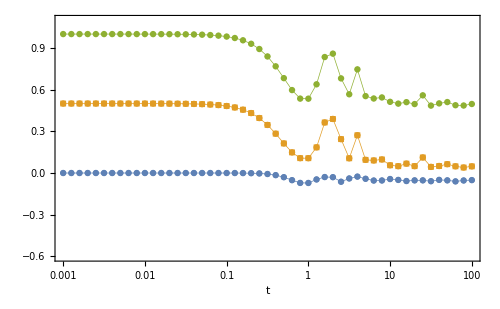

```mathematica
ListLogLinearPlot[Transpose[{Power[10.,Range[-3,2,0.1]],#}]&/@{t2,t3,1/2+t2+t3},
PlotRange->{{10^(-3),10^2},{-0.6,1.1}},
Joined->True,
PlotMarkers->{Automatic,6},
PlotStyle->Directive[Thickness[0.001]],
Mesh->All,
GridLines->{Table[10^x,{x,-2,2}],Table[y,{y,-0.5,1,0.25}]},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],None},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->500
]
```

```mathematica
Calcular el PR!!!!
```

```mathematica
Table[
Sum[
Braket[KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenvecsH[[l]]]*Braket[eigenvecsH[[k]],KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E]]*Exp[-I(eigenvalsH[[k]]-eigenvalsH[[l]])t]*Conjugate[eigenvecsH[[l]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2^(L-1)]].eigenvecsH[[k]]
,{k,2^L},{l,2^L}]
,{i,0,1},{j,0,1}]
```

$Aborted

```mathematica
{k,l,t,i,j}={200,1094,50,0,1};
Braket[KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenvecsH[[l]]]*Braket[eigenvecsH[[k]],KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E]]*Exp[-I(eigenvalsH[[k]]-eigenvalsH[[l]])t]*Conjugate[eigenvecsH[[l]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2^(L-1)]].eigenvecsH[[k]]
```

-7.18494×10^-11-4.30573×10^-11 ⅈ

```mathematica
{k,l,t,i,j}={1094,200,50,0,1};
Braket[KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenvecsH[[l]]]*Braket[eigenvecsH[[k]],KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j}],ψ0E]]*Exp[-I(eigenvalsH[[k]]-eigenvalsH[[l]])t]*Conjugate[eigenvecsH[[l]]].KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2^(L-1)]].eigenvecsH[[k]]
```

4.76373×10^-14-1.49145×10^-14 ⅈ

```mathematica
{{0,1},{0,0}}.{{a,b},{c,d}}.{{0,0},{1,0}}//MatrixForm
```

(d | 0
0 | 0)

```mathematica
ρ=Outer[Times,#,#]&[Normalize@{1,0,0,1}]
```

{{1/2,0,0,1/2},{0,0,0,0},{0,0,0,0},{1/2,0,0,1/2}}

```mathematica
#.ρ.ConjugateTranspose[#]&[KroneckerProduct[{{0,1},{0,0}},IdentityMatrix[2]]]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 1/2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
MatrixPartialTrace[KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].KroneckerProduct[{{a,b},{c,d}},Dyad[{p,q}]].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]],1,2]
```

{{0,0},{0,0}}

```mathematica
MatrixPartialTrace[KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].Outer[Times,{1/√2,0,0,1/√2},{1/√2,0,0,1/√2}].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]],1,2]
```

{{0,0},{0,0}}

```mathematica
MatrixPartialTrace[KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].Outer[Times,{a,b,c,d},{a,b,c,d}].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]],1,2]
```

{{0,0},{0,0}}

```mathematica
KroneckerProduct[{{1,0},{0,0}},IdentityMatrix[2]].Outer[Times,{a,b,c,d},{a,b,c,d}].KroneckerProduct[{{0,0},{0,1}},IdentityMatrix[2]]
```

{{0,0,a c,a d},{0,0,b c,b d},{0,0,0,0},{0,0,0,0}}

```mathematica
Sum[1/2^10 Exp[-I(eigenvalsH[[i]]-eigenvalsH[[j]])1],{i,2048},{j,2048}]
```

0.0955229-3.4148×10^-15 ⅈ

```mathematica
Exp[I Pi]
```

-1

```mathematica
Exp[I Pi-I Pi/4]
```

ⅇ^((3 ⅈ π)/4)

```mathematica
numerosComplejos=Flatten[Table[Exp[-I (eigenvalsH[[i]]-eigenvalsH[[j]])1],{i,1050,1150},{j,1050,1150}]];
```

```mathematica
numerosComplejos=Flatten[Table[Exp[-I (eigenvalsH[[i]]+eigenvalsH[[k]]-eigenvalsH[[j]]-eigenvalsH[[l]])1],{i,1050,1060},{j,1050,1060},{l,1050,1060},{l,1050,1060}]];
```

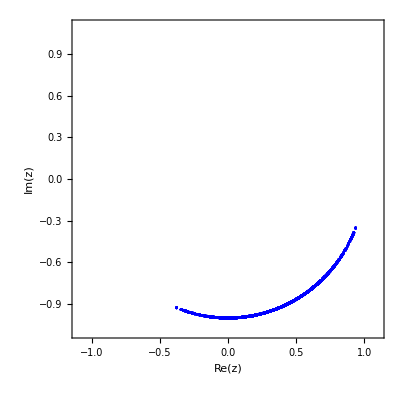

```mathematica
(*Graficar puntos en el plano complejo*)
Graphics[{PointSize[0.005],Style[Point[{Re[#],Im[#]}],Blue]&/@numerosComplejos},
PlotRange->{{-1.1,1.1},{-1.1,1.1}},
Axes->True,AxesOrigin->{0,0},Frame->True,FrameLabel->{"Re(z)","Im(z)"},PlotRange->All,AspectRatio->1]
```

```mathematica
50^2
```

2500

```mathematica
10^4
```

10000

## 3. Investigando el 2do y 3er término de eq:appendix:A:4 viendo qué hay dentro de la sumatoria sobre i y j

Se encontró que dentro de la sumatoria los sumandos que aportan más en el segundo término sin importar regular o caótico son aquellos i=j (puntos amarilos están abajo de los verdes y los celestes abajo de los rojos): 

Falta investigar qué pasa en para el tercer término.

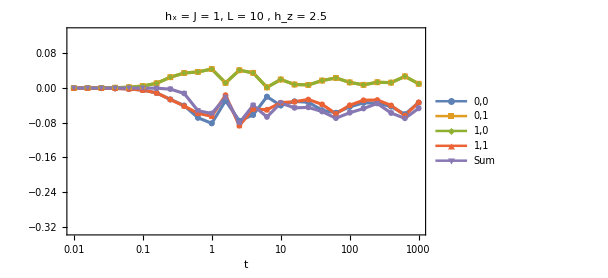
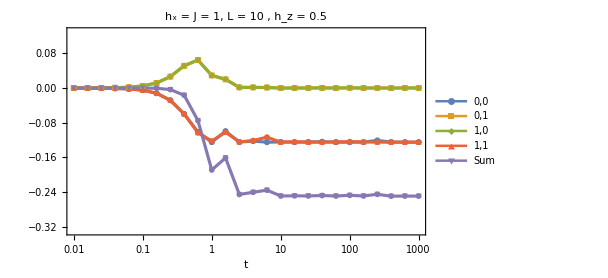

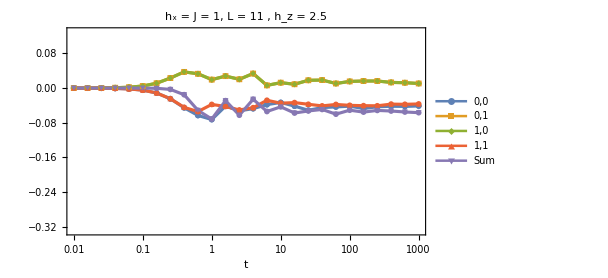
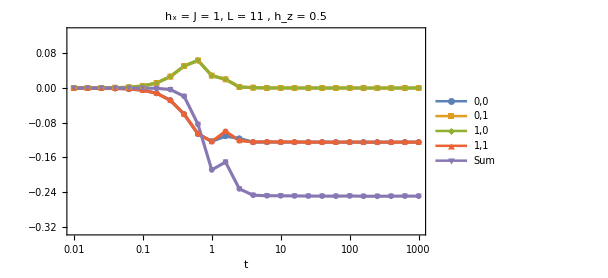

## 3.1. Definiciones de esta sección

```mathematica
(* Calcular el segundo término *)ClearAll[t2eqAppA4]
t2eqAppA4[L_,hx_,hz_,J_,t_,ψ0E_]:=
Module[{H,eigenvalsH,eigenvecsH},
(* Calcular los eigenvalores y eigenvectores del Hamiltoniano *)
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];

Table[
-1/2*Chop[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]*Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{2,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]
]
,{i,2},{j,2}]
]
```

```mathematica
(* Calcular el tercer término *)
ClearAll[t3eqAppA4]
t3eqAppA4[L_,hx_,hz_,J_,t_,ψ0E_]:=
Module[{H,eigenvalsH,eigenvecsH},
(* Calcular los eigenvalores y eigenvectores del Hamiltoniano *)
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];

Table[
1/2*Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]
]
```

## 3.2. Cálculos

```mathematica
timeValues=Power[10,Range[-2,3,0.2]];
```

```mathematica
(* Establecer parámetros que no voy a modificar *)
L=9(*number of spins*);
{hx,J}={1.,1.};
```

```mathematica
figs={};
```

```mathematica
(* Generar un estado aleatorio para el entorno *)
SeedRandom[32372];(*32372 fue la primer semilla*)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
t2=Table[t2eqAppA4[L,hx,hz=2.5,J,t,ψ0E],{t,timeValues}];
```

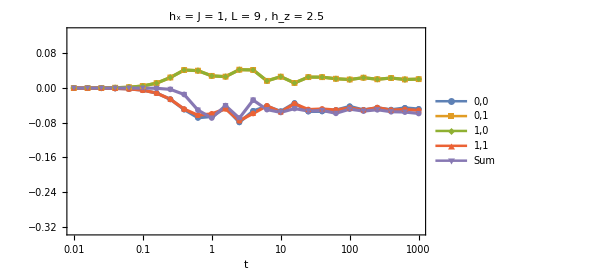
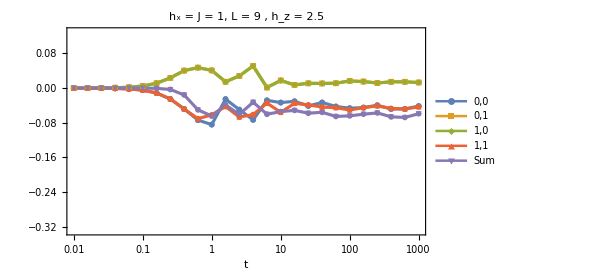

```mathematica
AppendTo[figs,ListLogLinearPlot[Transpose[{timeValues,#}]&/@Join[Transpose[Flatten/@t2],{Total[Flatten/@t2,{2}]}],
PlotRange->{{10^-2,10^3},{-0.33,0.13}},
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
PlotMarkers->{Automatic,6},
Mesh->All,
GridLines->{Table[10^x,{x,-2,4}],Table[y,{y,-0.5,1,0.1}]},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],None},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->450,
PlotLegends->{"0,0","0,1","1,0","1,1","Sum"},
PlotLabel->Style["h_x = J = 1, L = "<>ToString[L]<>" , h_z = "<>ToString[hz],Black,FontSize->24]
]
];

(* Mostrar figuras *)
figs
```

```mathematica
t2eqAppA4[L,hx,hz=2.5,J,14.2,ψ0E]
```

{{-0.0327072,0.0105031},{0.0105031,-0.0576896}}

```mathematica
figs={};
```

```mathematica
(* Generar un estado aleatorio para el entorno *)
SeedRandom[32373];(*32372 fue la primer semilla*)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
t2=Table[t2eqAppA4[L,hx,hz=0.5,J,t,ψ0E],{t,timeValues}];
```

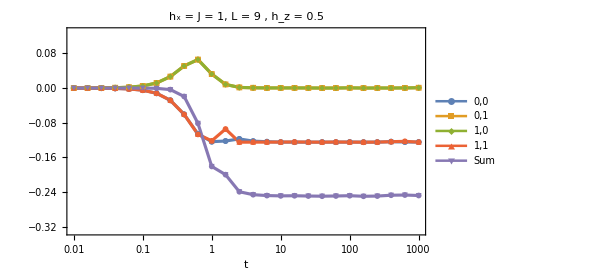
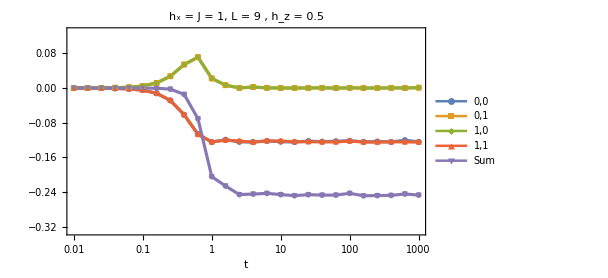

```mathematica
AppendTo[figs,ListLogLinearPlot[Transpose[{timeValues,#}]&/@Join[Transpose[Flatten/@t2],{Total[Flatten/@t2,{2}]}],
PlotRange->{{10^-2,10^3},{-0.33,0.13}},
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
PlotMarkers->{Automatic,6},
Mesh->All,
GridLines->{Table[10^x,{x,-2,4}],Table[y,{y,-0.5,1,0.1}]},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],None},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->450,
PlotLegends->{"0,0","0,1","1,0","1,1","Sum"},
PlotLabel->Style["h_x = J = 1, L = "<>ToString[L]<>" , h_z = "<>ToString[hz],Black,FontSize->24]
]
];

(* Mostrar figuras *)
figs
```

Los términos i=j son los que aportan más sin importar regular o caótico (puntos amarilos están abajo de los verdes y los celestes abajo de los rojos):

```mathematica
¨{,}
```

{-Graphics-,-Graphics-}

```mathematica
{,}
```

{-Graphics-,-Graphics-}

```mathematica
hz=2.5
```

2.5

```mathematica
figs={};
```

```mathematica
(* Generar un estado aleatorio para el entorno *)
SeedRandom[32376];(*32372 fue la primer semilla*)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
t3=Table[t3eqAppA4[L,hx,hz=2.5,J,t,ψ0E],{t,timeValues}];
```

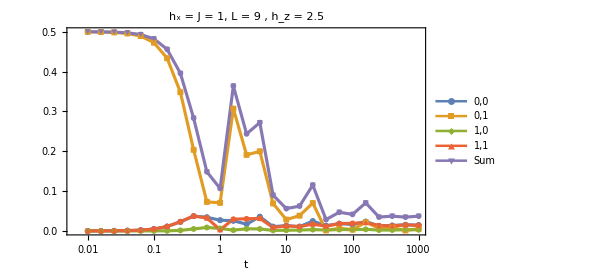
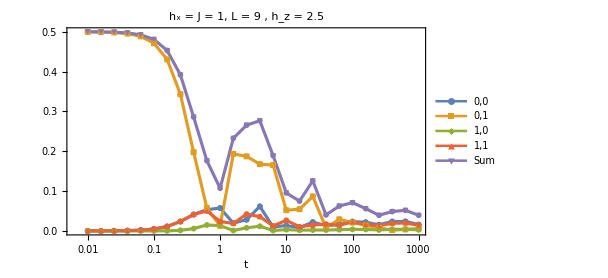
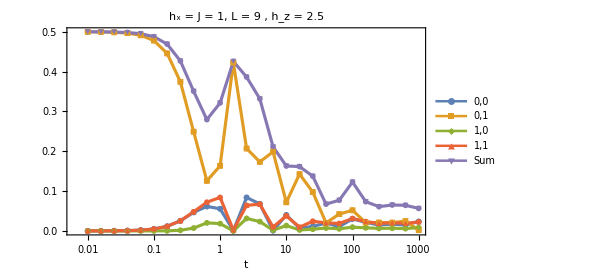
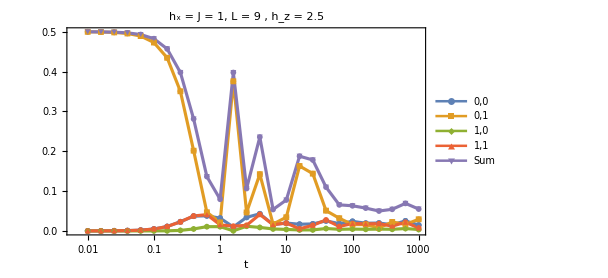
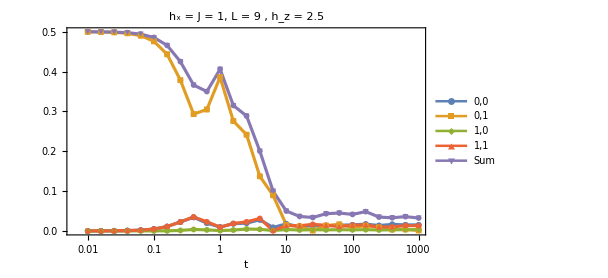
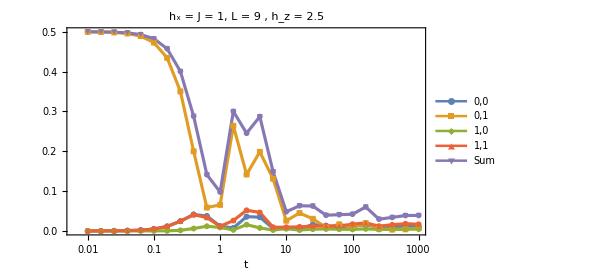

```mathematica
AppendTo[figs,ListLogLinearPlot[Transpose[{timeValues,#}]&/@Join[Transpose[Flatten/@t3],{Total[Flatten/@t3,{2}]}],
(*PlotRange->{{10^-2,10^3},{-0.33,0.13}}*)
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
PlotMarkers->{Automatic,6},
Mesh->All,
GridLines->{Table[10^x,{x,-2,4}],Table[y,{y,-0.5,1,0.1}]},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],None},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->450,
PlotLegends->{"0,0","0,1","1,0","1,1","Sum"},
PlotLabel->Style["h_x = J = 1, L = "<>ToString[L]<>" , h_z = "<>ToString[hz],Black,FontSize->24]
]
];

(* Mostrar figuras *)
figs
```

```mathematica
hz=0.5
```

0.5

```mathematica
figs={};
```

```mathematica
(* Generar un estado aleatorio para el entorno *)
SeedRandom[32376];(*32372 fue la primer semilla*)
ψ0E=RandomChainProductState[L-1];
```

```mathematica
t3=Table[t3eqAppA4[L,hx,hz=0.5,J,t,ψ0E],{t,timeValues}];
```

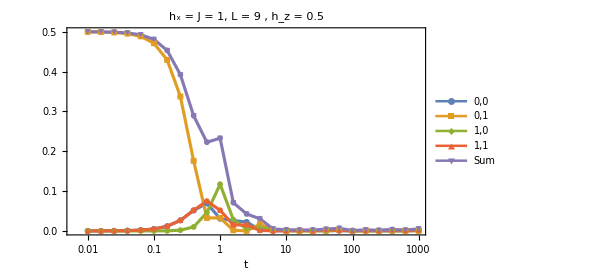
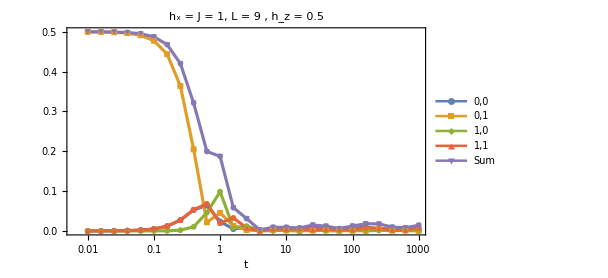
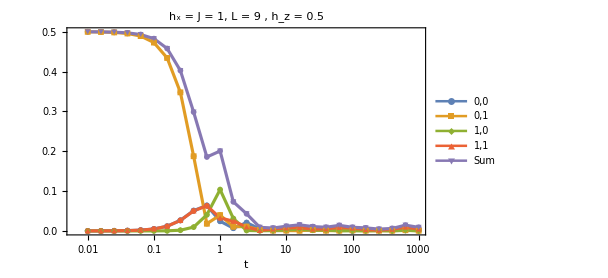
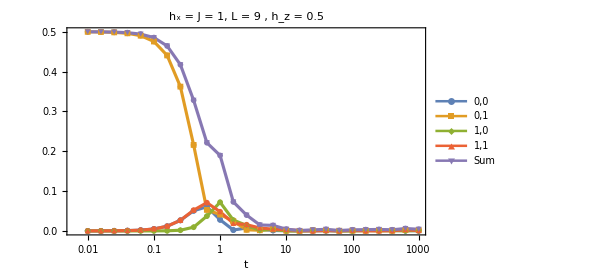
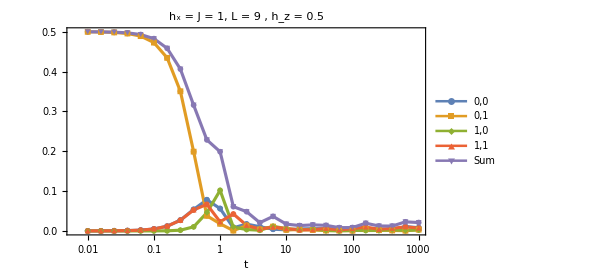
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
AppendTo[figs,ListLogLinearPlot[Transpose[{timeValues,#}]&/@Join[Transpose[Flatten/@t3],{Total[Flatten/@t3,{2}]}],
PlotRange->Full,
(*PlotRange->{{10^-2,10^3},{-0.33,0.13}}*)
Joined->True,
PlotStyle->Directive[Thickness[0.005]],
PlotMarkers->{Automatic,6},
Mesh->All,
GridLines->{Table[10^x,{x,-2,4}],Table[y,{y,-0.5,1,0.1}]},
GridLinesStyle->Directive[Gray,Dashed],
Frame->True,
FrameLabel->{TraditionalForm[HoldForm[t]],None},
FrameTicks->{{Automatic,None},{myTicks,None}},
LabelStyle->Directive[Black,FontFamily->"Arial",FontSize->22],
ImageSize->450,
PlotLegends->{"0,0","0,1","1,0","1,1","Sum"},
PlotLabel->Style["h_x = J = 1, L = "<>ToString[L]<>" , h_z = "<>ToString[hz],Black,FontSize->24]
]
];

(* Mostrar figuras *)
figs
```

```mathematica
t3eqAppA4[L,hx,hz=0.5,J,0.01,ψ0E]
```

{{0.0000499893,0.499781},{4.99946×10^-9,0.0000499893}}

```mathematica
(* Calcular los eigenvalores y eigenvectores del Hamiltoniano *)
H=IsingNNOpenHamiltonian[hx=1,hz=0.5,J=1,L=9];
{eigenvalsH,eigenvecsH}=N[Chop[Eigensystem[H]]];

t=0.01;

Table[
1/2*Abs[
Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i-1}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,2}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{j-1}],ψ0E],eigenvalsH,eigenvecsH]]^2
,{i,2},{j,2}]
```

{{0.0000499893,0.499781},{4.99946×10^-9,0.0000499893}}

```mathematica
i=0;t=20.01;Conjugate[StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenvalsH,eigenvecsH]].KroneckerProduct[SparseArray[{1,1}->1,{2,2}],IdentityMatrix[2^(L-1)]].StateEvolution[t,KroneckerVectorProduct[VectorFromKetInComputationalBasis[{i}],ψ0E],eigenvalsH,eigenvecsH]
```

0.547886+0. ⅈ

```mathematica
Tr[{{1,0},{0,0}}.Pauli[#]]&/@{0,1,2,3}
```

{1,0,0,1}

```mathematica
x=0.05;Sqrt[1-4x]
```

0.894427

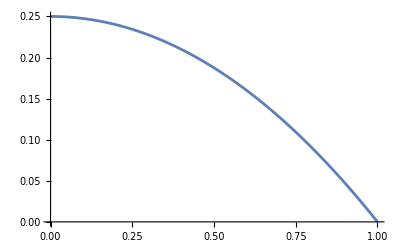

```mathematica
Plot[1/4(1-x^2),{x,0,1}]
```